## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.2; Q=0.8;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.175355-1.23941×10^-6 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.1

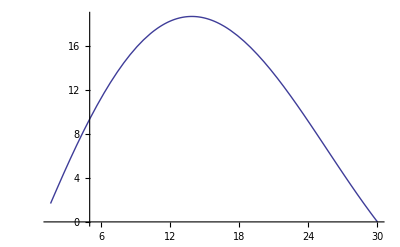

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-1.23946×10^-6},{30.2,-1.1848×10^-6},{30.4,-1.13298×10^-6},{30.6,-1.08376×10^-6},{30.8,-1.03701×10^-6},{31.,-9.92582×10^-7},{31.2,-9.50335×10^-7},{31.4,-9.1021×10^-7},{31.6,-8.71972×10^-7},{31.8,-8.35596×10^-7},{32.,-8.00981×10^-7},{32.2,-7.68023×10^-7},{32.4,-7.36581×10^-7},{32.6,-7.06701×10^-7},{32.8,-6.78173×10^-7},{33.,-6.50966×10^-7},{33.2,-6.25018×10^-7},{33.4,-6.00274×10^-7},{33.6,-5.76645×10^-7},{33.8,-5.54087×10^-7},{34.,-5.32544×10^-7},{34.2,-5.11965×10^-7},{34.4,-4.92301×10^-7},{34.6,-4.73503×10^-7},{34.8,-4.5553×10^-7},{35.,-4.38321×10^-7},{35.2,-4.21882×10^-7},{35.4,-4.0615×10^-7},{35.6,-3.91132×10^-7},{35.8,-3.76674×10^-7},{36.,-3.62869×10^-7},{36.2,-3.49646×10^-7},{36.4,-3.36971×10^-7},{36.6,-3.24824×10^-7},{36.8,-3.13183×10^-7},{37.,-3.02019×10^-7},{37.2,-2.9131×10^-7},{37.4,-2.81041×10^-7},{37.6,-2.71154×10^-7},{37.8,-2.61724×10^-7},{38.,-2.52603×10^-7},{38.2,-2.43925×10^-7},{38.4,-2.35552×10^-7},{38.6,-2.27476×10^-7},{38.8,-2.19743×10^-7},{39.,-2.12345×10^-7},{39.2,-2.05187×10^-7},{39.4,-1.98355×10^-7},{39.6,-1.91741×10^-7},{39.8,-1.85387×10^-7},{40.,-1.79272×10^-7},{40.2,-1.73397×10^-7},{40.4,-1.67733×10^-7},{40.6,-1.62259×10^-7},{40.8,-1.57023×10^-7},{41.,-1.51992×10^-7},{41.2,-1.47101×10^-7},{41.4,-1.42442×10^-7},{41.6,-1.37913×10^-7},{41.8,-1.3355×10^-7},{42.,-1.29377×10^-7},{42.2,-1.25311×10^-7},{42.4,-1.21409×10^-7},{42.6,-1.17648×10^-7},{42.8,-1.14024×10^-7},{43.,-1.10522×10^-7},{43.2,-1.07143×10^-7},{43.4,-1.03899×10^-7},{43.6,-1.00684×10^-7},{43.8,-9.77073×10^-8},{44.,-9.47818×10^-8},{44.2,-9.19497×10^-8},{44.4,-8.92075×10^-8},{44.6,-8.65624×10^-8},{44.8,-8.40108×10^-8},{45.,-8.15579×10^-8},{45.2,-7.9163×10^-8},{45.4,-7.68538×10^-8},{45.6,-7.4626×10^-8},{45.8,-7.2474×10^-8},{46.,-7.0391×10^-8},{46.2,-6.83741×10^-8},{46.4,-6.64245×10^-8},{46.6,-6.45423×10^-8},{46.8,-6.27153×10^-8},{47.,-6.09495×10^-8},{47.2,-5.92441×10^-8},{47.4,-5.75818×10^-8},{47.6,-5.59849×10^-8},{47.8,-5.44361×10^-8},{48.,-5.29367×10^-8},{48.2,-5.1479×10^-8},{48.4,-5.007×10^-8},{48.6,-4.86973×10^-8},{48.8,-4.73769×10^-8},{49.,-4.60994×10^-8},{49.2,-4.48585×10^-8},{49.4,-4.36532×10^-8},{49.6,-4.24843×10^-8},{49.8,-4.13528×10^-8},{50.,-4.02511×10^-8},{50.2,-3.9187×10^-8},{50.4,-3.81617×10^-8},{50.6,-3.71631×10^-8},{50.8,-3.61898×10^-8},{51.,-3.52455×10^-8},{51.2,-3.43329×10^-8},{51.4,-3.34462×10^-8},{51.6,-3.25867×10^-8},{51.8,-3.17677×10^-8},{52.,-3.09331×10^-8},{52.2,-3.01485×10^-8},{52.4,-2.94027×10^-8},{52.6,-2.86366×10^-8},{52.8,-2.79148×10^-8},{53.,-2.72199×10^-8},{53.2,-2.65352×10^-8},{53.4,-2.58723×10^-8},{53.6,-2.52303×10^-8},{53.8,-2.4601×10^-8},{54.,-2.39989×10^-8},{54.2,-2.34112×10^-8},{54.4,-2.28365×10^-8},{54.6,-2.22773×10^-8},{54.8,-2.17365×10^-8},{55.,-2.12128×10^-8},{55.2,-2.06963×10^-8},{55.4,-2.01978×10^-8},{55.6,-1.97139×10^-8},{55.8,-1.92434×10^-8},{56.,-1.87872×10^-8},{56.2,-1.83378×10^-8},{56.4,-1.7903×10^-8},{56.6,-1.74802×10^-8},{56.8,-1.70729×10^-8},{57.,-1.66703×10^-8},{57.2,-1.62824×10^-8},{57.4,-1.59022×10^-8},{57.6,-1.55328×10^-8},{57.8,-1.51724×10^-8},{58.,-1.4824×10^-8},{58.2,-1.4439×10^-8},{58.4,-1.41497×10^-8},{58.6,-1.3827×10^-8},{58.8,-1.35125×10^-8},{59.,-1.32091×10^-8},{59.2,-1.29065×10^-8},{59.4,-1.26155×10^-8},{59.6,-1.2332×10^-8},{59.8,-1.20566×10^-8},{60.,-1.17863×10^-8}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

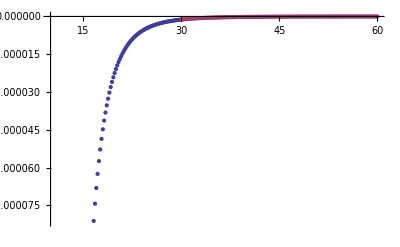

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

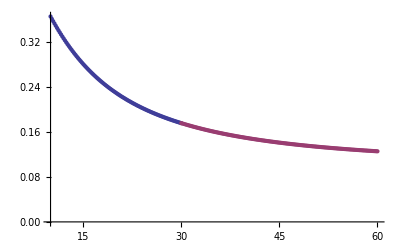

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.2/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.2/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.2/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.2/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```